```mathematica
underFive=Import["/Users/murilo/Master_programs/UoA/DataScience/Exams/Test1/fusion_GLOBAL_DATAFLOW_UNICEF_1.0_WORLD.CME_MRY0T4._T..csv",{"Data"}];
Dimensions[underFive]
```

{45,22}

```mathematica
underFiveYearValue=underFive[[2;;,5;;6]]
```

{{1980,118.471},{1981,115.03},{1982,111.796},{1983,110.909},{1984,108.886},{1985,106.214},{1986,103.077},{1987,99.3883},{1988,98.6713},{1989,95.4738},{1990,93.5817},{1991,93.3107},{1992,92.6932},{1993,90.7796},{1994,89.6173},{1995,87.752},{1996,85.9544},{1997,83.9693},{1998,82.2868},{1999,79.3487},{2000,76.6715},{2001,74.0977},{2002,71.4819},{2003,68.6062},{2004,66.216},{2005,63.3284},{2006,60.6212},{2007,58.0469},{2008,55.8012},{2009,54.0241},{2010,51.7098},{2011,50.6236},{2012,47.8162},{2013,46.1188},{2014,44.8822},{2015,43.7221},{2016,42.4015},{2017,41.3165},{2018,40.1752},{2019,39.4722},{2020,38.738},{2021,38.2399},{2022,38.249},{2023,36.7189}}

```mathematica
(* NOt necessary for the exam 2026 underFiveYearValueClean1=underFiveYearValue/.{a_,b_}:> {ToExpression[StringSplit[a,"-"]],b}/.{{a_,b_},c_}:>  {a,c} *)
```

```mathematica
Dimensions[%]
```

{44,2}

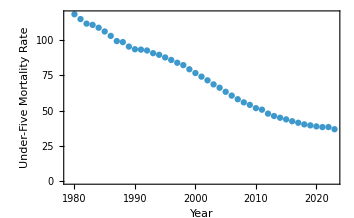

```mathematica
ListPlot[underFiveYearValue,Frame-> True,FrameLabel->{"Year","Under-Five Mortality Rate"}]
```

```mathematica
mykeys={"Year","World Mean"};
```

```mathematica
tosave=Prepend[underFiveYearValue,mykeys];
```

```mathematica
(* Not necessary for exam 2026 Export["/Users/murilo/Master_programs/UoA/DataScience/Exams/Test1/Unicef-under-five-mortability2025.csv",tosave,{"CSV"}]*)
```

```mathematica
Dimensions[tosave]
```

{44,2}

```mathematica
underFive20192023=underFiveYearValue[[40;;44,All]]
```

{{2019,39.4722},{2020,38.738},{2021,38.2399},{2022,38.249},{2023,36.7189}}

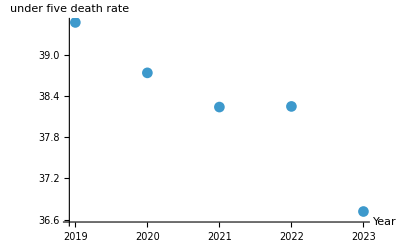

```mathematica
ListPlot[underFive20192023,AxesLabel->{"Year","under five death rate"},PlotMarkers->Automatic]
```

```mathematica
(*we could have estimated the slope by doing*)
```

```mathematica
slope=(underFive20192023[[5,2]]-underFive20192023[[1,2]])/5
```

-0.550669

```mathematica
model1=LinearModelFit[underFive20192023,x,x]
```

FittedModel[…]

```mathematica
model1[2024]
```

36.4849

```mathematica
underFive20222023=underFiveYearValue[[43;;44,All]]
```

{{2022,38.249},{2023,36.7189}}

```mathematica
model2=LinearModelFit[underFive20222023,x,x]
```

FittedModel[…]

```mathematica
model2[2024]
```

35.1887

```mathematica
model2[2024]-underFiveYearValue[[44,2]]
```

-1.53018